```mathematica
pUnrep:=1200.0;
Kd:=800.0;
n:=3.0;

taur:=120.0;
taup:=3600.0;
b:=10.0;
gr=Log[2]/taur;
gp=Log[2]/taup;
kp=b*gr;
krmax:=pUnrep*gr*gp/kp;

kr[p_]:=krmax/(1.0+(p/Kd)^n)

optGen = {Frame->True,FrameStyle->Directive[Black,Thick],RotateLabel->False,PlotStyle->AbsoluteThickness[3],LabelStyle->Directive[35,FontFamily->"Palatino Linotype",Black]}; 
imSize = {ImageSize->800};
optLab=FrameLabel->{"p",Text[Style[ToExpression["k_r(p)",TeXForm,HoldForm]]]};
```

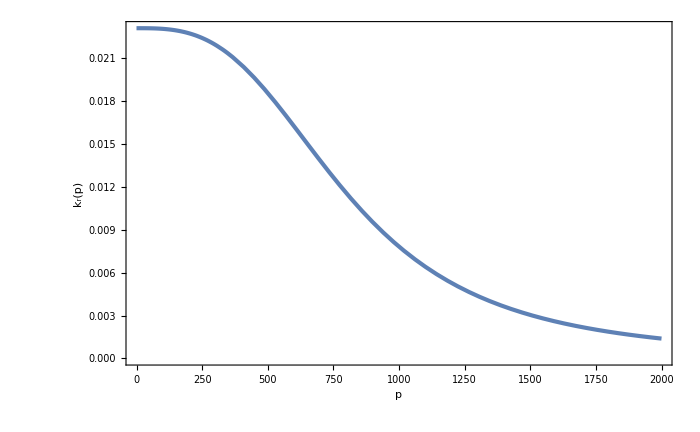

```mathematica
Show[Plot[kr[x],{x,0,2000},Evaluate[optGen],Evaluate[optLab]],ImageSize->700]
```

```mathematica
krmax
```

(480. Log^2)/(g_r tau_p tau_r)